```mathematica
Define two vectors on the sphere in 2D, we linearize around q
```

```mathematica
x[t_]={Cos[t],Sin[t]}
```

{Cos[t],Sin[t]}

```mathematica
q[s_]={Cos[s],Sin[s]}
```

{Cos[s],Sin[s]}

```mathematica
x'[t]
```

{-Sin[t],Cos[t]}

```mathematica
g[t_,s_]=q[s].x[t]
```

Cos[s] Cos[t]+Sin[s] Sin[t]

```mathematica
g[1,2]
```

Cos[1] Cos[2]+Sin[1] Sin[2]

```mathematica
f[t_,s_]=ArcCos[g[t,s]]/Sin[ArcCos[g[t,s]]]
```

ArcCos[g[t,s]]/(√(1-g[t,s]^2))

```mathematica
f'[t]
```

f'[t]

```mathematica
h is the Log_x of q
```

```mathematica
h[t_,s_]=(x[t]-q[s]g[t,s])f[t,s]
```

{(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] (Cos[t]-Cos[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(√(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2)),(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] (Sin[t]-Sin[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(√(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2))}

```mathematica
D[h[t,s],t]
```

{(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] (Cos[t] Sin[s]-Cos[s] Sin[t]) (Cos[s] Cos[t]+Sin[s] Sin[t]) (Cos[t]-Cos[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2)^(3/2)-((Cos[t] Sin[s]-Cos[s] Sin[t]) (Cos[t]-Cos[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2)+(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] (-Sin[t]-Cos[s] (Cos[t] Sin[s]-Cos[s] Sin[t])))/(√(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2)),(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] (Cos[t] Sin[s]-Cos[s] Sin[t]) (Cos[s] Cos[t]+Sin[s] Sin[t]) (Sin[t]-Sin[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2)^(3/2)-((Cos[t] Sin[s]-Cos[s] Sin[t]) (Sin[t]-Sin[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2)+(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] (Cos[t]-Sin[s] (Cos[t] Sin[s]-Cos[s] Sin[t])))/(√(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2))}

```mathematica
hNorth [t_,s_]={{Cos[-s],-Sin[-s]},{Sin[-s],Cos[-s]}}.h[t,s]
```

{(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] Cos[s] (Cos[t]-Cos[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(√(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2))+(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] Sin[s] (Sin[t]-Sin[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(√(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2)),-(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] Sin[s] (Cos[t]-Cos[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(√(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2))+(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] Cos[s] (Sin[t]-Sin[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(√(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2))}

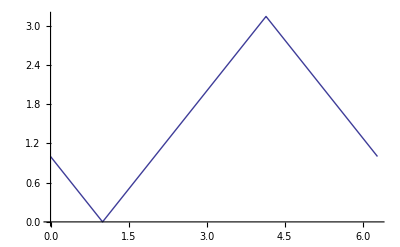

```mathematica
Plot[Norm[hNorth[t,1.],2],{t,0,2Pi}]
```

```mathematica
Plot3D[Norm[hNorth[t,s],2],{t,0,2Pi},{s,0,2Pi}]
```

Power::infy: Infinite expression 1/√0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/√0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/√0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

-Graphics3D-

```mathematica
hNorth0 [t_,s_]={Cos[-s],-Sin[-s]}.h[t,s]
```

(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] Cos[s] (Cos[t]-Cos[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(√(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2))+(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] Sin[s] (Sin[t]-Sin[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(√(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2))

```mathematica
hNorth1 [t_,s_]={Sin[-s],Cos[-s]}.h[t,s]
```

-(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] Sin[s] (Cos[t]-Cos[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(√(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2))+(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] Cos[s] (Sin[t]-Sin[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(√(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2))

```mathematica
Plot3D[hNorth0[t,s],{t,0,2Pi},{s,0,2Pi}]
```

-Graphics3D-

```mathematica
This clearly is the 0component of x in the tangent plane at the north pole
```

```mathematica
Plot3D[hNorth1[t,s],{t,0,2Pi},{s,0,2Pi}]
```

-Graphics3D-

```mathematica
Integrate[hNorth1[t,s],{s,0,2Pi}]
```

```mathematica
2 π (π+ArcCos[Cos[t]] Csc[t] √(Sin[t]^2))
```

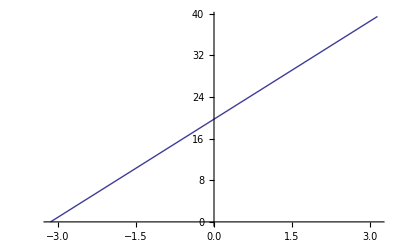

```mathematica
Plot[2 π (π+ArcCos[Cos[t]] Csc[t] √(Sin[t]^2)),{t,-Pi,Pi}]
```

```mathematica
Gauss[x_,Sig_]=1/Sqrt[2Pi*Sig]Exp[-0.5x^2/Sig]
```

(ⅇ^(-(0.5 x^2)/Sig))/(√(2 π) √Sig)

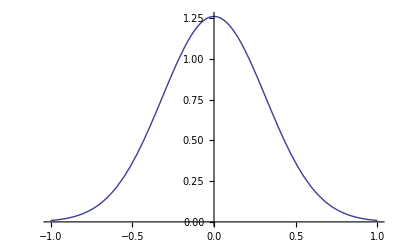

```mathematica
Plot[Gauss[x,0.1],{x,-1,1}]
```

```mathematica
GaussInTnorth[t_,s_,Sig_]=Gauss[hNorth1[t,s],Sig]
```

1/(√(2 π) √Sig)ⅇ^(-(0.5 (-(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] Sin[s] (Cos[t]-Cos[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(√(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2))+(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] Cos[s] (Sin[t]-Sin[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(√(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2)))^2)/Sig)

```mathematica
Plot3D[GaussInTnorth[t,s,.1],{t,-Pi,Pi},{s,-Pi,Pi}]
```

-Graphics3D-

```mathematica
Integrate[1/(√(2 π) √Sig)ⅇ^(-(0.5 (-(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] Sin[s] (Cos[t]-Cos[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(√(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2))+(ArcCos[Cos[s] Cos[t]+Sin[s] Sin[t]] Cos[s] (Sin[t]-Sin[s] (Cos[s] Cos[t]+Sin[s] Sin[t])))/(√(1-(Cos[s] Cos[t]+Sin[s] Sin[t])^2)))^2)/Sig),{t,-Pi,Pi}]
```

-0.5 Csc[3.14159×10^-9-1. s] Erf[1/(√Sig)(1.11072-0.707107 ArcSin[(1.+0. ⅈ) Cos[(1.+0. ⅈ) s]+(3.14159×10^-9+0. ⅈ) Sin[(1.+0. ⅈ) s]])] √(Sin[3.14159×10^-9-1. s]^2)+0.5 Csc[3.14159-1. s] Erf[1/(√Sig)(1.11072+0.707107 ArcSin[(1.+0. ⅈ) Cos[(1.+0. ⅈ) s]-(3.14159×10^-9+0. ⅈ) Sin[(1.+0. ⅈ) s]])] √(Sin[3.14159-1. s]^2)-0.5 Csc[3.14159×10^-9+s] Erf[1/(√Sig)(1.11072-0.707107 ArcSin[(1.+0. ⅈ) Cos[(1.+0. ⅈ) s]-(3.14159×10^-9+0. ⅈ) Sin[(1.+0. ⅈ) s]])] √(Sin[3.14159×10^-9+s]^2)+0.5 Csc[3.14159+s] Erf[1/(√Sig)(1.11072+0.707107 ArcSin[(1.+0. ⅈ) Cos[(1.+0. ⅈ) s]+(3.14159×10^-9+0. ⅈ) Sin[(1.+0. ⅈ) s]])] √(Sin[3.14159+s]^2)

```mathematica
Sig:=10
```

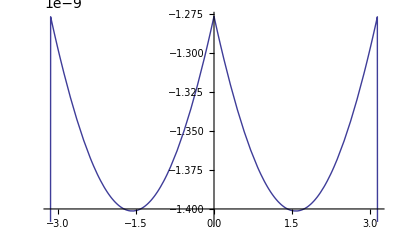

```mathematica
Plot[-0.5000000000000001 Csc[3.141592653589793*^-9-1. s] Erf[(1.1107207345395915-0.7071067811865475 ArcSin[(1.+0. ⅈ) Cos[(1.+0. ⅈ) s]+(3.1415926554037345*^-9+0. ⅈ) Sin[(1.+0. ⅈ) s]])/(√Sig)] √(Sin[3.141592653589793*^-9-1. s]^2)+0.5000000000000001 Csc[3.1415926504482004-1. s] Erf[(1.1107207345395915+0.7071067811865475 ArcSin[(1.+0. ⅈ) Cos[(1.+0. ⅈ) s]-(3.1415928873394554*^-9+0. ⅈ) Sin[(1.+0. ⅈ) s]])/(√Sig)] √(Sin[3.1415926504482004-1. s]^2)-0.5000000000000001 Csc[3.141592653589793*^-9+s] Erf[(1.1107207345395915-0.7071067811865475 ArcSin[(1.+0. ⅈ) Cos[(1.+0. ⅈ) s]-(3.1415926554037345*^-9+0. ⅈ) Sin[(1.+0. ⅈ) s]])/(√Sig)] √(Sin[3.141592653589793*^-9+s]^2)+0.5000000000000001 Csc[3.1415926504482004+s] Erf[(1.1107207345395915+0.7071067811865475 ArcSin[(1.+0. ⅈ) Cos[(1.+0. ⅈ) s]+(3.1415928873394554*^-9+0. ⅈ) Sin[(1.+0. ⅈ) s]])/(√Sig)] √(Sin[3.1415926504482004+s]^2),{s,-Pi,Pi}]
```

```mathematica
Plot3D[-0.5000000000000001 Csc[3.141592653589793*^-9-1. s] Erf[1/(√Sig)(1.1107207345395915-0.7071067811865475 ArcSin[(1.+0. ⅈ) Cos[(1.+0. ⅈ) s]+(3.1415926554037345*^-9+0. ⅈ) Sin[(1.+0. ⅈ) s]])] √(Sin[3.141592653589793*^-9-1. s]^2)+0.5000000000000001 Csc[3.1415926504482004-1. s] Erf[1/(√Sig)(1.1107207345395915+0.7071067811865475 ArcSin[(1.+0. ⅈ) Cos[(1.+0. ⅈ) s]-(3.1415928873394554*^-9+0. ⅈ) Sin[(1.+0. ⅈ) s]])] √(Sin[3.1415926504482004-1. s]^2)-0.5000000000000001 Csc[3.141592653589793*^-9+s] Erf[1/(√Sig)(1.1107207345395915-0.7071067811865475 ArcSin[(1.+0. ⅈ) Cos[(1.+0. ⅈ) s]-(3.1415926554037345*^-9+0. ⅈ) Sin[(1.+0. ⅈ) s]])] √(Sin[3.141592653589793*^-9+s]^2)+0.5000000000000001 Csc[3.1415926504482004+s] Erf[1/(√Sig)(1.1107207345395915+0.7071067811865475 ArcSin[(1.+0. ⅈ) Cos[(1.+0. ⅈ) s]+(3.1415928873394554*^-9+0. ⅈ) Sin[(1.+0. ⅈ) s]])
] √(Sin[3.1415926504482004+s]^2),{s,-Pi,Pi},{Sig,0.0001,10.0}]
```

-Graphics3D-

```mathematica
Itnegral seems to be very 0 all over the place!
```